# Analysis of Packing V3E07L1N01T1_1

Three Vertices, Seven Edges, 1 Loop, Combinatorial Number 01, Face Pattern 1, Type 1

```mathematica
-Graphics-;
```

The following equation is based on the rhombus in the center of the flat torus.We use the fact that the rhombus breaks into four equal triangles that are all in terms of rb, since we know the relationship between rs and rb.Note that we cannot explicitly solve for rb, rs; trigonometry doesn't tell us exactly where the sides are broken up between rs and rb, so the triangles could be dilated to any degree while still obeying the same relationships.Thus, solving gives us the angle x, which can be then used to find α.

```mathematica
-Graphics-;
```

```mathematica
Solve[{Sin[x]==((-1+√2) (1/2))/((1/2)+(-1+√2) (1/2)),Tan[x]==((-1+√2) (1/2))/(√(((-1+√2) (1/2)+(1/2))^2-((-1+√2) (1/2))^2))},{x}]
```

{{x→ConditionalExpression[ArcTan[(-3+2 √2)/(√(-1+2 √2)-√(2 (-1+2 √2)))]+2 π C[1],C[1]∈ℤ]}}

π = 2 (θ) + 2 (x)

```mathematica
Simplify[(Pi-2(ArcTan[(-3+2 √2)/(√(-1+2 √2)-√(2 (-1+2 √2)))]))/2]
```

1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])

This is θ!!

Now, we can use the exact same coordinate system for V3E7L0N1T11.  Note that (x2c,y2c) are the coordinates of the small circle Circle 2, and (x3c, y3a) are the coordinates of the small circle Circle 3.

```mathematica
y2c:=((L/2)*Sin[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]-(1/Tan[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])])((1/2)-(L/2)*Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]))
```

```mathematica
y3a:=((L/2)*Sin[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]-(1/Tan[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])])((L*Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]+(1/2))-((L/2)*Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]+1)))
```

```mathematica
x2c:=(1/2)
```

```mathematica
x3c:=(L*Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]+(1/2))
```

We haven’t specified edge lengths, so we do that now.

```mathematica
Solve[(x2c)^2+(y2c)^2==(1/Sqrt[2])^2,L]
```

{{L→(Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])] Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2-√(2 Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2 Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Sin[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2))/(2 Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2 Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Sin[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2)},{L→(Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])] Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+√(2 Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2 Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Sin[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2))/(2 Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2 Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Sin[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2)}}

```mathematica
N[Solve[(x2c)^2+(y2c)^2==(1/Sqrt[2])^2,L]]
```

{{L→-0.663252},{L→1.24904}}

Second solutions is positive so it is correct.  So now we don’t have any variables, and we can simply substitute in for L.

```mathematica
Simplify[(Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])] Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+√(2 Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2 Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Sin[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2))/(2 Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2 Cot[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2+Sin[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])]^2)]
```

(1+√(-2+4 √2)+Cos[2 ArcTan[(-1+√2)/(√(-1+2 √2))]]-√(1+Cos[2 ArcTan[(-1+√2)/(√(-1+2 √2))]]))/(√(-2+4 √2))

```mathematica
FullSimplify[y2c/.L-> (1+√(-2+4 √2)+Cos[2 ArcTan[(-1+√2)/(√(-1+2 √2))]]-√(1+Cos[2 ArcTan[(-1+√2)/(√(-1+2 √2))]]))/(√(-2+4 √2))]
```

1/2

```mathematica
FullSimplify[y3a/.L-> (1+√(-2+4 √2)+Cos[2 ArcTan[(-1+√2)/(√(-1+2 √2))]]-√(1+Cos[2 ArcTan[(-1+√2)/(√(-1+2 √2))]]))/(√(-2+4 √2))]
```

-1+√2+1/2 √(-11+8 √2)

## Circle Centers and Radii

```mathematica
centers = {{0,0},
{(1/2),
(1/2)},
{1/2 (3-2 √2+√(-11+8 √2))+(1/2),
-1+√2+1/2 √(-11+8 √2)}}
```

{{0,0},{1/2,1/2},{1/2+1/2 (3-2 √2+√(-11+8 √2)),-1+√2+1/2 √(-11+8 √2)}}

## Lattice Vectors

We are working this flat torus

```mathematica
latticeVectors = {
 {1,0},
{ 1/2 (3-2 √2+√(-11+8 √2)),(7-7/(√(-1+2 √2))+√(14+28 √2))/(2+4 √2)}};
```

## Edges

Here we store the edges a list {i,j,m,n} where center[[i]] is connected to center[[j]] + m*latticeVectors[[1]] + n*latticeVectors[2]]
center[[i]] is *always* in the fundamental domain ****the last two numbers are winding numbers****

```mathematica
edges = {{1,2,0,0},{1,1,1,0},{2,3,0,0},{2,1,0,1},{2,1,1,0},{3,1,0,1},{3,1,1,1},{3,1,1,0}};
```

### Check the edge lengths are all 2rs= Sqrt[2]-1 or rs+rb=Sqrt[2]rb=Sqrt[2]/2=1/Sqrt[2]

```mathematica
For[i=1,i≤Length[edges],i++,Print["Edge ",i,": Length is ",FullSimplify[
EuclideanDistance[centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]]]]]
```

Edge 1: Length is 1/(√2)

Edge 2: Length is 1

Edge 3: Length is -1+√2

Edge 4: Length is 1/(√2)

Edge 5: Length is 1/(√2)

Edge 6: Length is 1/(√2)

Edge 7: Length is 1/(√2)

Edge 8: Length is 1/(√2)

Yes!

## Packing Visualization

Here we visualize the packing and the fundamental domain to help determine the value of the parameters for which this is a packing graph.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,5Pi/6,"α"},Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{{b,5Pi/6,"β"},Pi/2+ArcCos[2 (-1+√2)]/2,Pi},AnimationRunning -> False
]
```

## Locally Maximally Dense

We have to determine for which values of α and β the packing is locally maximally dense. To be locally maximally dense (Following Connelly, Rigid Circle and Sphere Packings, Page 51, Theorem 6.1)
	1. The packing graph is rigid as a bar framework
	2. Have a proper stress that is non-zero on every member

### Rigid as bar framework

To be rigid as a bar framework we need to establish a rigid ordering of the circles. The numbering of the circles in the picture above is a rigid ordering of the packing disks -- See Lemma 6.2 in the Connelly paper on Rigid Sphere and Circle Packings. Note: The first is held fixed.

### Proper Stress

Assign a scalar to each edge of the packing and collect those scalars in a vector called ω. We need to solve the linear algebra problem where the sum of the ω_i times the vector from vertex j is zero.

```mathematica
Animate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{α->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{α->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{α->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{α->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{α->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{α->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{α->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["α",Small],centers[[2]]/.{α->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{α->a,β->b},Offset[{10,-10},{0,0}]]}},(*Angle Markers Labels*)
Table[Text[Style[Subscript["ω",i],Large,Red],1/2*(centers[[edges[[i,1]] ]]+centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]])/.{α->a,β->b}],{i,1,Length[edges]}](*Label Edges With Stresses*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{α->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{a,5Pi/6,"α"},Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{{b,5Pi/6,"β"},Pi/2+ArcCos[2 (-1+√2)]/2,Pi},AnimationRunning -> False
]
```

```mathematica
equations = Table[{0,0},{k,Length[centers]}]; (*Start with the zero equations*)
w =Table[Subscript[ω,i],{i,Length[edges]}]; (*Initialize a vector of Subscript[ω, i]*)
For[i=1,i≤Length[centers], i++, (*i is the center number*)
For[j=1,j≤Length[edges], j++, (*j is the edge number*)
If[edges[[j,1]]==i, (*center i is the starting point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(centers[[edges[[j,1]] ]]-centers[[edges[[j,2]] ]]-
edges[[j,3]]*latticeVectors[[1]]-
edges[[j,4]]*latticeVectors[[2]])] 
If[edges[[j,2]]==i, (*center i is the ending point of edge j*)
equations[[i]] = equations[[i]]+w[[j]]*(-centers[[edges[[j,1]] ]]+centers[[edges[[j,2]] ]]+
edges[[j,3]]*latticeVectors[[1]]+
edges[[j,4]]*latticeVectors[[2]])]
]
]
stresses = Flatten[Simplify[Solve[Flatten[equations]==Flatten[Table[{0,0},{k,Length[centers]}]],w]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ω_1→(2 √(43-30 √2) (1+2 √2) ω_3+(-7+7 √2+2 √(86-60 √2)+√(43-30 √2)) ω_4)/(2 √(-1+2 √2) (1+2 √2)),ω_5→(-3+2 √2) ω_3+1/2 (-4+4 √2-7/(√(-1+2 √2) (1+2 √2))+√(-2+4 √2)-√(-11+8 √2)) ω_4,ω_7→(2 √(43-30 √2) (1+2 √2) ω_3+(2 √(86-60 √2)+8 √(43-30 √2)+7 (-6+4 √2-3 √(-1+2 √2)+2 √(-2+4 √2)-√(-11+8 √2)+√(-22+16 √2))) ω_6)/(42-28 √2+2 √(86-60 √2)-6 √(43-30 √2)+33 √(-1+2 √2)-18 √(-2+4 √2)+7 √(-11+8 √2)-7 √(-22+16 √2)),ω_8→(2 √(43-30 √2) (1+2 √2) ω_3-(3-2 √2+√(-11+8 √2)) (42-28 √2+2 √(86-60 √2)-6 √(43-30 √2)+33 √(-1+2 √2)-18 √(-2+4 √2)+7 √(-11+8 √2)-7 √(-22+16 √2)) ω_3-2 (7-7 √2+2 √(86-60 √2)+√(43-30 √2)-√(-1+2 √2)-2 √(-2+4 √2)) (2-2 √2+√(-11+8 √2)) ω_6)/((2-2 √2+√(-11+8 √2)) (42-28 √2+2 √(86-60 √2)-6 √(43-30 √2)+33 √(-1+2 √2)-18 √(-2+4 √2)+7 √(-11+8 √2)-7 √(-22+16 √2)))}

Notice that stress ω_3, ω_4, ω_6, is free.

```mathematica
yuck := Simplify[equations /. stresses] (*check the solutions, Should output all zeros but I don't think Mathematica can simplify it*)
```

```mathematica
N[Simplify[yuck/.{Subscript[ω, 6]-> 1,Subscript[ω, 4]-> 1,Subscript[ω, 3]-> 1}]]
```

{{-2.19634×10^-14,3.36354×10^-13},{0.,0.},{-4.25856×10^-14,-5.91602×10^-13}}

```mathematica
N[Simplify[stresses/.{Subscript[ω, 6]-> 1,Subscript[ω, 4]-> 1,Subscript[ω, 3]-> 1}]]
```

{ω_1→1.12019,ω_5→0.656854,ω_7→1.35219,ω_8→1.41421}

## Moduli Space Of Locally Maximally Dense Packings

Determine the Torus Angle and Ratio for the packings that are locally maximally dense.

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]]]
```

ArcCos[1-1/(√2)]

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]]]
```

√(1+√(-11+8 √2))

Now plot the region of the moduli space that is covered by (r,theta)=(torusRatio,torusAngle). The right boundary is in the region, the others are not.

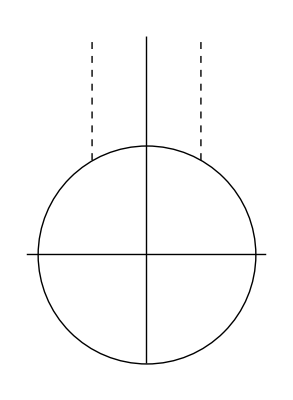

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{α,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},{β,Pi/2+ArcCos[2 (-1+√2)]/2,Pi},RegionFunction->(#4>#3 &)]
]
```

It’s hard to see, but there is a little dot in the moduli space which corresponds to this packing.

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ]
```

1/56 (-7+21 √2-√(-1001+742 √2)) π

```mathematica
N[torusDensity]
```

0.883311